## 1. PRAKTIKA

### 1. ARIKETA

```mathematica
T1=Table[Sqrt[8*i],{i,1,50}]
```

{2 √2,4,2 √6,4 √2,2 √10,4 √3,2 √14,8,6 √2,4 √5,2 √22,4 √6,2 √26,4 √7,2 √30,8 √2,2 √34,12,2 √38,4 √10,2 √42,4 √11,2 √46,8 √3,10 √2,4 √13,6 √6,4 √14,2 √58,4 √15,2 √62,16,2 √66,4 √17,2 √70,12 √2,2 √74,4 √19,2 √78,8 √5,2 √82,4 √21,2 √86,4 √22,6 √10,4 √23,2 √94,8 √6,14 √2,20}

```mathematica
T1[[12]]
```

4 √6

```mathematica
T1[[49]]/T1[[50]]
```

7/(5 √2)

### 2. ARIKETA

#### ·)

```mathematica
g[x_,y_]=Cos[x^3+y^3]/(x-y+1)
```

Cos[x^3+y^3]/(1+x-y)

```mathematica
f[x_] = x^3-2x+1
```

1-2 x+x^3

```mathematica
h[x_]=x^2-3x+2
```

2-3 x+x^2

#### a)

```mathematica
g[Pi,2 Pi]
```

Cos[9 π^3]/(1-π)

```mathematica
N[g[Pi,2 Pi]]
```

0.399233

#### b)

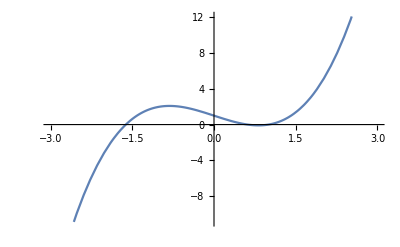

```mathematica
Plot[f[x], {x,-3,3}]
```

#### c)

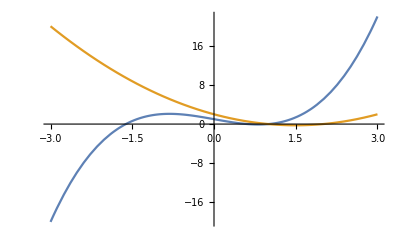

```mathematica
Plot[{f[x],h[x]}, {x,-3,3}]
```

### 3. ARIKETA

#### a)

```mathematica
c={{4,1,3,1,3},{2,6,3,-1,2},{1,3,4,1,1},{-4,5,4,2,-3},{1,-1,-3,-1,2}}
```

{{4,1,3,1,3},{2,6,3,-1,2},{1,3,4,1,1},{-4,5,4,2,-3},{1,-1,-3,-1,2}}

```mathematica
MatrixForm[c]
```

(4 | 1 | 3 | 1 | 3
2 | 6 | 3 | -1 | 2
1 | 3 | 4 | 1 | 1
-4 | 5 | 4 | 2 | -3
1 | -1 | -3 | -1 | 2)

```mathematica
Part[Transpose[c],3] // MatrixForm
```

(3
3
4
4
-3)

#### b)

```mathematica
c[[{2,3,4,5},{1,2,4,5}]] // MatrixForm
```

(2 | 6 | -1 | 2
1 | 3 | 1 | 1
-4 | 5 | 2 | -3
1 | -1 | -1 | 2)

#### c)

```mathematica
Inverse[c] // MatrixForm
```

(91/120 | 7/24 | -4/3 | 5/24 | -9/20
41/120 | 5/24 | -2/3 | 7/24 | 1/20
-21/40 | -1/8 | 1 | -3/8 | -3/20
7/8 | -1/8 | -1 | 5/8 | 1/4
-67/120 | -7/24 | 4/3 | -5/24 | 13/20)

### 4. ARIKETA

#### a)

```mathematica
e={{1,1,1,1},{-m,1,1,2},{1,-m,1,3},{1,1,-m,4}}
```

{{1,1,1,1},{-m,1,1,2},{1,-m,1,3},{1,1,-m,4}}

```mathematica
v=Flatten[e]
```

{1,1,1,1,-m,1,1,2,1,-m,1,3,1,1,-m,4}

#### b)

```mathematica
Solve[Det[e]==0,m]
```

{{m→-7},{m→-1},{m→-1}}

```mathematica
MatrixRank[e/.m-> -7]
```

3

```mathematica
MatrixRank[e/.m-> -1]
```

2

#### c)

```mathematica
Inverse[e/.m->2] // MatrixForm
```

(1/3 | -8/27 | 1/27 | 1/27
1/3 | 2/27 | -7/27 | 2/27
1/3 | 1/9 | 1/9 | -2/9
0 | 1/9 | 1/9 | 1/9)

#### d)

```mathematica
MatrixPower[e/.m->-1,5] // MatrixForm
```

(778 | 778 | 778 | 2332
1037 | 1037 | 1037 | 3110
1296 | 1296 | 1296 | 3888
1555 | 1555 | 1555 | 4666)

### 5. ARIKETA

#### a)

```mathematica
d={{1,a,-1,1},{2,1,-a,2},{1,-1,-1,a-1}}
```

{{1,a,-1,1},{2,1,-a,2},{1,-1,-1,-1+a}}

```mathematica
minoreak=Minors[d,3]
```

{{2+a-a^2,-2+5 a-2 a^2,-4+4 a-a^2,2 a+a^2-a^3}}

```mathematica
zerrenda=Flatten[minoreak]
```

{2+a-a^2,-2+5 a-2 a^2,-4+4 a-a^2,2 a+a^2-a^3}

```mathematica
dSol=Solve[zerrenda=={0,0,0,0},a]
```

{{a→2}}

```mathematica
d2=d/.dSol[[1]]
```

{{1,2,-1,1},{2,1,-2,2},{1,-1,-1,1}}

```mathematica
MatrixRank[d2]
```

2

#### b)

```mathematica
db=d[[{2,3},{1,3}]]
```

{{2,-a},{1,-1}}

```mathematica
MatrixRank[db/.a->3]
```

2

#### c)

```mathematica
minoreakd=Minors[d/.a->2,2]
```

{{-3,0,0,-3,3,0},{-3,0,0,-3,3,0},{-3,0,0,-3,3,0}}